```mathematica
Import[FileNameJoin[{NotebookDirectory[],"modules/breed.m"}]];
Import[FileNameJoin[{NotebookDirectory[],"modules/fitfunctions.m"}]];
Import[FileNameJoin[{NotebookDirectory[],"modules/generators.m"}]];
Import [FileNameJoin[{NotebookDirectory[],"modules/phenotypes.m"}]];
```

# Script Start

```mathematica
(*Algorithm Configuration*)
(*imgData=Import[SystemDialogInput["FileOpen"]];*)
imgData = Import[FileNameJoin[{NotebookDirectory[],"mountains_desert1.png"}]];
fitnessPlots=Null;Dynamic[fitnessPlots]
matingText = Null; Dynamic[matingText]
performanceText = Null; Dynamic[performanceText]
allImages = Null; Dynamic[allImages]


fittestIndex = -1;
fittestHistory = {}; Dynamic[fittestHistory]

showDebug = False;
nsteps = 4000;
detectionThreshold= 0.5;
numGenoms  = 10;
numCurves = 20;
bezierOrder=3;
resolution = 6;
dimensions = 2;

pcross = 0.8;
nextGenFrac = 0.6;
pmut = 0.01;

(*Calculated Configuration*)
replaceN = IntegerPart[numGenoms*nextGenFrac];
imgSpace = ImageDimensions[imgData];

totalFitness = Table[0,{i,1,nsteps}];
maxFitness = Table[0,{i,1,nsteps}];

genotypeLength = numCurves*dimensions*bezierOrder*resolution;
ffitfunc = FFitFuncGen[imgData,"edges"];

(*Start, Beginning of Evolution*)
genotypes = BinPopGenerator [numGenoms,genotypeLength];

Do[
timeTotal = AbsoluteTime[];

timeSVG = AbsoluteTiming[
phenotypes = ParallelTable[BezierPhenotype[genotypes⟦i⟧, numCurves, dimensions, bezierOrder, resolution, imgSpace ], {i, 1,numGenoms}];
graphics = ParallelTable[Graphics[BezierCurve[phenotypes⟦i⟧, SplineDegree->bezierOrder-1],PlotRange->{{0,imgSpace⟦1⟧},{0,imgSpace⟦2⟧}}, ImageSize->imgSpace], {i, 1,numGenoms}];
rastered = ParallelTable[Rasterize[graphics⟦i⟧], {i, 1,numGenoms}];
];
timeRaster = AbsoluteTiming[
pixels = ParallelTable[PixelValuePositions[rastered⟦i⟧,Black,detectionThreshold], {i, 1,numGenoms}];
];

timefitness = AbsoluteTiming[
fitness = ParallelTable[ffitfunc[ pixels⟦i⟧],{i, 1,numGenoms}];
];

timeBreed = AbsoluteTiming[

If[RandomReal[]<0.25,
p1Index=SelectParentByWheel[genotypes, fitness];
p2Index=SelectParentByWheel[genotypes, fitness];,
p1Index = Ordering[fitness,-1]⟦1⟧;
p2Index = Ordering[fitness,-2]⟦1⟧;
];
p1 = genotypes⟦p1Index⟧;
p2 = genotypes⟦p2Index⟧;
lowestN = Ordering[fitness,replaceN];
children = Table[ Breed [p1, p2, genotypeLength, pcross],{i,1,replaceN}];
Do[genotypes⟦lowestN⟦i⟧⟧ = children⟦i⟧;, {i,1,replaceN}];

mutateN = numGenoms-2;
mutationList =  Ordering[fitness,mutateN];
Do[genotypes⟦mutationList⟦i⟧⟧= Mutate[genotypes⟦mutationList⟦i⟧⟧, genotypeLength, pmut], {i,1,mutateN}];
];


timeEvaluate = AbsoluteTiming[
maxFitness⟦iteration⟧ = Max[fitness];
totalFitness⟦iteration⟧ = Fold[Plus,0,fitness] ;

fitnessPlots = Grid[{{ListPlot[totalFitness⟦1 ;; iteration⟧,ImageSize->Medium ],
ListPlot[maxFitness⟦1 ;; iteration⟧,ImageSize->Medium]}}
];

allImages = graphics;

If[Ordering[fitness,-1]⟦1⟧  ≠ fittestIndex, 
fittestIndex = Ordering[fitness,-1]⟦1⟧;
fittestHistory =  Show[imgData,ColorReplace[ColorReplace[graphics⟦fittestIndex⟧,Black-> Pink,0.5], White]];
(*AppendTo[fittestHistory,  Show[imgData,ColorReplace[ColorReplace[graphics⟦fittestIndex⟧,Black-> Pink,0.5], White]]];*)
];
];

timeTotal = AbsoluteTime[]-timeTotal; 
performanceText = Text["Step: ",iteration, " of ",nsteps," ", "Parents:",p1Index," ", p2Index ,
 " [T ffit:", timefitness⟦1⟧,
 ", T total:",timeTotal,
", T SVG:", timeSVG⟦1⟧,
", T Raster:", timeRaster⟦1⟧,
", T Eval:", timeEvaluate⟦1⟧,
", T Breed:",timeBreed⟦1⟧, "]"];
matingText = Text["Step: ", iteration, " Parents are " ,p1Index" and ", p2Index];

, {iteration, 1,nsteps}
];
```

Calculated imArr, should only happen once

$Aborted

```mathematica
DynamicModule[{pts={{0,0}},a=10,i=1,func},
func[]:=Do[AppendTo[pts,{i,i}]Print["test", i];,{i,a}];

Dynamic@Grid[{{ListPlot[pts,PlotRange->All],SpanFromLeft,SpanFromLeft},
{Slider[Dynamic[a],{10,20,1}],ProgressIndicator[i,{1,a}],
Button["Run",pts={{0,0}};func[],Method->"Queued"]}}
]
]
```

```mathematica
fittestIndex
```

8

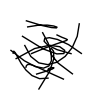

```mathematica
graphics⟦fittestIndex⟧
```

```mathematica
{1,2,3,4,5}⟦1 ;; 3⟧
```

{1,2,3}